```mathematica
incr[digs_,base_]:=Module[{carry=1,ndigs=digs,k=1,nd},While[k≤Length[digs],{carry,nd}=QuotientRemainder[ndigs⟦k⟧+carry,base⟦k⟧];ndigs⟦k⟧=nd;If[carry==0,Break[]];k=k+1;];ndigs];
BNArrange[BNB_,conf_,string_]:=Module[{i,cont,k,res,supp},cont=1;res={};For[i=1,i≤Length[string],i++,supp=Table[BNB⟦i,conf⟦k⟧⟧,{k,cont,cont+string⟦i⟧-1}];cont=cont+string⟦i⟧;AppendTo[res,supp];];res];
SelBNB[BNB_]:=Module[{i,j,check},check=0;For[i=1,i≤Length[BNB],i++,For[j=1,j≤Length[BNB⟦i⟧]-1,j++,If[BNB⟦i,j⟧≥BNB⟦i,j+1⟧,check=1;];];];check];
GenPI[BNconf_]:=Module[{i,supp,supp1,fin},fin={};For[i=1,i≤Length[BNconf],i++,supp=-BNconf⟦i⟧;supp1=Sort[Join[supp,BNconf⟦i⟧]];AppendTo[fin,supp1];];fin];
t[i_,j_]:=2. Min[i,j]-1. KroneckerDelta[i,j];
UpB[L_,M_,α_,n_]:=(L-1.-∑_(j=1.)^M t[n,j] α⟦j⟧)/2.;
GenString[M_]:=Block[{part,part1,pair,d,j,k,m,p,check},m=M;part=Reap[While[m≠0,d=IntegerPart[RandomReal[{1.,M+1-1/10^12}]];j=IntegerPart[RandomReal[{1.,M+1-1/10^12}]];p=RandomReal[{0,1}];If[p≤(d PartitionsP[m-j d])/(m PartitionsP[m]),Sow[Table[d,{k,1,j}]];m=m-j d;];];];part1=Flatten[part];Table[Count[part1,i],{i,1,M}]];
ChooString[M_,L_,strOl_]:=Block[{string,mat,DDol,DDne,i,j,strNe,p,vec,vec1},string=strOl;mat=Table[t[i,j],{i,1,M},{j,1,M}];DDol=∏_(i=1)^M Binomial[L-Total[Table[mat⟦i,j⟧ string⟦j⟧,{j,1,M}]],string⟦i⟧];strNe=GenString[M];DDne=∏_(i=1)^M Binomial[L-Total[Table[mat⟦i,j⟧ strNe⟦j⟧,{j,1,M}]],strNe⟦i⟧];p=RandomReal[{0,1}];If[p≤Min[1,DDne/DDol],string=strNe;];string];
BTsel[M_,L_,α_]:=Block[{J,n,k},J=Table[RandomSample[Table[k,{k,-UpB[L,M,α,n],UpB[L,M,α,n]}],α⟦n⟧],{n,1,M}];J];
Theta[x_,m_,n_]:=If[n≠m,2 ArcTan[x/Abs[n-m]]+4 Sum[ArcTan[x/(Abs[n-m]+k)],{k,2,n+m-Abs[n-m]-2,2}]+2 ArcTan[x/(n+m)],4 Sum[ArcTan[x/k],{k,2,2 n-2,2}]+2 ArcTan[x/(2 n)]];
SolveBethe[M_,L_,string_,BN_]:=Block[{sol,x,n,g,b,m,o,h,check,sol1,bit,EE,EE1,EE2,EE3},check=1;bit=0;sol=Quiet[Table[x[n][g],{n,1,M},{g,1,string⟦n⟧}]/.FindRoot[Flatten[Table[ArcTan[(x[n][g])/n]-(π BN⟦n,g⟧)/L-(∑_(m=1)^M ∑_(b=1)^string⟦m⟧ If[m≠n||b≠g,Theta[x[n][g]-x[m][b],m,n],0])/(2 L)==0,{n,1,M},{g,1,string⟦n⟧}]],Flatten[Table[{x[o][h],RandomReal[]},{o,1,M},{h,1,string⟦o⟧}],1],WorkingPrecision->15,MaxIterations->200,AccuracyGoal->15]];check=Flatten[Table[ArcTan[(sol⟦n⟧⟦g⟧)/n]-(π BN⟦n,g⟧)/L-(∑_(m=1)^M ∑_(b=1)^string⟦m⟧ If[m≠n||b≠g,Theta[sol⟦n⟧⟦g⟧-sol⟦m⟧⟦b⟧,m,n],0])/(2 L),{n,1,M},{g,1,string⟦n⟧}]];If[Total[Abs[check]]>1/10^11,Print["Findroot failed with string"];Print[BN];bit=1;];EE=If[M≠0,+Total[Flatten[Table[(2. n)/(sol⟦n,g⟧^2.+n^2.),{n,1,M},{g,1,string⟦n⟧}]]],-L/4];{bit,EE,BN,Chop[sol]}];
PIState[string_,BN_]:=Module[{BN1,BN2,i,check,tot},BN1=Table[Sort[-BN⟦i⟧],{i,1,Length[BN]}];BN2=Flatten[BN1];check=Select[BN2,Abs[#1]<1/10^13&];tot=Select[Flatten[BN],Abs[#1]>0&];If[BN==BN1&&check=={},0,1]];
NonZeroRap[rap_]:=Module[{rap1,check},rap1=Flatten[rap];check=Select[rap1,Abs[#1]<1/10^12&];If[check=={},0,1]];
Dtheta[x_,n_]:=(2 n)/(n^2+x^2);
DTheta[x_,m_,n_]:=If[n≠m,(2 Abs[m-n])/(x^2+Abs[m-n]^2)+4 Sum[(k+Abs[m-n])/(x^2+(k+Abs[m-n])^2),{k,2,n+m-Abs[n-m]-2,2}]+(2 (m+n))/((m+n)^2+x^2),4 Sum[k/(k^2+x^2),{k,2,2 n-2,2}]+(4 n)/(4 n^2+x^2)];
PP[x_,n_]:=Module[{k},If[OddQ[n],(x ∏_(k=0)^Floor[n/2] ((2 k+1)^2+x^2)/((2 k)^2+x^2))/(4^n √(n^2+x^2)),If[Abs[Re[x]]>10^-13,(√(n^2+x^2) ∏_(k=0)^(Floor[n/2]-1) ((2 k)^2+x^2)/((2 k+1)^2+x^2))/(4^n x),(-1)^(n/2+1)n 2^(-2n) ∏_(k=1)^(Floor[n/2]-1) (2 k)^2/(2 k+1)^2]]];
PPMG[x_,n_]:=Module[{k},If[OddQ[n],2^n (x^2+n^2) ∏_(k=0)^Floor[n/2] 1/(((2 k+1)^2+x^2)^2),If[Abs[Re[x]]>10^-13,2^n x^2 (x^2+n^2) ∏_(k=0)^(n/2) 1/(((2 k)^2+x^2)^2),I/n 2^(n/2)(-1)^(n/2+1)∏_(k=1)^(n/2-1) 1/(2k)^2]]];
CGm[i1_,j1_,i2_,j2_,string_,rap_]:=Module[{k,l},If[i1≠i2||j1≠j2,2 (DTheta[rap⟦i1,j1⟧-rap⟦i2,j2⟧,i1,i2]-DTheta[rap⟦i1,j1⟧+rap⟦i2,j2⟧,i1,i2]),2 (L-1) Dtheta[rap⟦i1,j1⟧,i1]-4 ∑_(k=1)^(i1-1) Dtheta[rap⟦i1,j1⟧,k]-2 ∑_(k=1)^Length[string] ∑_(l=1)^string⟦k⟧ If[i1≠k||j1≠l,DTheta[rap⟦i1,j1⟧-rap⟦k,l⟧,i1,k]+DTheta[rap⟦i1,j1⟧+rap⟦k,l⟧,i1,k],0]]];
CGp[i1_,j1_,i2_,j2_,string_,rap_]:=Module[{k,l},If[i1≠i2||j1≠j2,2 (DTheta[rap⟦i1,j1⟧-rap⟦i2,j2⟧,i1,i2]+DTheta[rap⟦i1,j1⟧+rap⟦i2,j2⟧,i1,i2]),2 L Dtheta[rap⟦i1,j1⟧,i1]-2 ∑_(k=1)^Length[string] ∑_(l=1)^string⟦k⟧ If[i1≠k||j1≠l,DTheta[rap⟦i1,j1⟧-rap⟦k,l⟧,i1,k]+DTheta[rap⟦i1,j1⟧+rap⟦k,l⟧,i1,k],0]]];
Overlap[string_,rap_,NI_]:=Module[{indx,ll,i,j,GGm,GGp},indx=Flatten[Table[Table[{i,j},{j,1,string⟦i⟧}],{i,1,Length[string]}],1];ll=Total[string];GGm=Table[CGm[indx⟦i,1⟧,indx⟦i,2⟧,indx⟦j,1⟧,indx⟦j,2⟧,string,rap],{i,1,ll},{j,1,ll}];GGp=Table[CGp[indx⟦i,1⟧,indx⟦i,2⟧,indx⟦j,1⟧,indx⟦j,2⟧,string,rap],{i,1,ll},{j,1,ll}];
Print[ √(Det[GGp]/Det[GGm])];
((√2 NI! (∏_(i=1)^Length[string] ∏_(j=1)^string⟦i⟧ PP[rap⟦i,j⟧,i]) √(Det[GGp]/Det[GGm]))/(√((2 NI)!)))^2];
OverlapMG[string_,rap_,M_]:=Module[{j},Overlap[string,rap,0] (∏_(i=1)^Length[string] ∏_(j=1)^string⟦i⟧ PPMG[rap⟦i,j⟧,i])^2];
KK1[x_]:=2/(x^2+1);
KK12[x_]:=1/(x^2+1/4);
Kp[x_,y_]:=KK1[x-y]+KK1[x+y];
Km[x_,y_]:=KK1[x-y]-KK1[x+y];
Gp[j_,k_,rap_]:=KroneckerDelta[j,k] (L KK12[rap⟦j⟧]-∑_(p=1)^Length[rap] Kp[rap⟦j⟧,rap⟦p⟧])+Kp[rap⟦j⟧,rap⟦k⟧];
Gm[j_,k_,rap_]:=KroneckerDelta[j,k] (L KK12[rap⟦j⟧]-∑_(p=1)^Length[rap] Kp[rap⟦j⟧,rap⟦p⟧])+Km[rap⟦j⟧,rap⟦k⟧];
index[string_,k_]:=Module[{z,cont},cont=1;z=k;While[z>0,z=z-string⟦cont⟧;cont++;];cont-1];
OverlapAll[string_,rap1_,NI_]:=Module[{rap,rapstring,rpstr1,k,ll,i,j,GGm,GGp},rapstring={};rap=Flatten[rap1];For[k=1,k≤Length[rap],k++,AppendTo[rapstring,Table[rap⟦k⟧/2+((1+RandomReal[{1/10^5,1/10^6}]) ⅈ (index[string,k]+1-2 j))/2.,{j,1,index[string,k]}]];];rpstr1=Flatten[rapstring];ll=Length[rpstr1];GGp=Table[Gp[i,j,rpstr1],{i,1,ll},{j,1,ll}];GGm=Table[Gm[i,j,rpstr1],{i,1,ll},{j,1,ll}];((√2 NI! (∏_(j=1)^ll (√(rpstr1⟦j⟧^2+1/4))/(4 rpstr1⟦j⟧)) √(Det[GGp]/Det[GGm]))/(√((2 NI)!)))^2];
L=8;
cont=0;
data=Reap[For[i=L/2,i≤L/2,i++,M=i;NI=L/2-i;base=Table[IntegerPart[M/j]+1,{j,1,M}];initial=Table[0,{k,1,M}];For[r=1,r≤∏_(b=1)^M base⟦b⟧,r++,If[∑_(s=1)^M s initial⟦s⟧==M,If[Total[EvenQ[initial]]==Length[initial] True,string=initial/2;BNBounds=Table[Table[kk,{kk,0.5,UpB[L,M,2 string,zz]}],{zz,1,Length[string]}];Lbounds=Table[Length[BNBounds⟦ii⟧],{ii,1,Length[BNBounds]}];BNbase=Flatten[Table[Table[Lbounds⟦ii⟧,{jj,1,string⟦ii⟧}],{ii,1,Length[string]}]];BNinit=Flatten[Table[0,{ii,1,Length[BNbase]}]];shift=Table[1,{ii,1,Length[BNbase]}];new1=BNinit+shift;For[rr=1,rr≤∏_(ii=1)^Length[BNbase] BNbase⟦ii⟧,rr++,x=BNArrange[BNBounds,new1,string];If[SelBNB[x]==0,BNPI=GenPI[x];sol=SolveBethe[M,L,initial,BNPI];If[sol⟦1⟧==0,rap1=Table[Sort[sol⟦4,k⟧],{k,1,Length[sol⟦4⟧]}];rap=Table[Table[-rap1⟦k,j⟧,{j,1,string⟦k⟧}],{k,1,Length[sol⟦4⟧]}];overlap=OverlapMG[string,rap,0];cont++;Print[cont];Sow[{string,sol⟦2⟧,Flatten[sol⟦3⟧],Flatten[sol⟦4⟧],overlap}];]];new=incr[BNinit,BNbase];BNinit=new;new1=new+shift;];];];initial1=incr[initial,base];initial=initial1;]]]⟦2⟧;
data1=Flatten[data,1];
Strconf=Table[data1⟦i,1⟧,{i,1,Length[data1]}];
BNumbers=Table[Flatten[data1⟦i,3⟧],{i,1,Length[data1]}];
Rapidities=Table[data1⟦i,4⟧,{i,1,Length[data1]}];
Obs=Table[{data1⟦i,2⟧,data1⟦i,5⟧},{i,1,Length[data1]}];
filename="/scratch/valba/Dimer/Rap_L"<>ToString[L]<>".dat";
filename1="/scratch/valba/Dimer/StrConf_L"<>ToString[L]<>".dat";
filename2="/scratch/valba/Dimer/Bnum_L"<>ToString[L]<>".dat";
filename3="/scratch/valba/Dimer/Obs_L"<>ToString[L]<>".dat";
(*Export[filename,Rapidities];
Export[filename1,Strconf];
Export[filename2,BNumbers];
Export[filename3,Obs];*)
```

1.1568280911944

1

1.3467132459255

2

```mathematica
(*MM=6;
initial={2,1,0,0,0,0};
BN={{-2.5,-1.5,1.5,2.5},{0},{},{},{},{}};
SolveBethe[MM,12,initial,BN]
OverlapMG[initial,{{0.58652891910193739745498164787655029977`15.,1.38101310763563718991715011361884236636`15.},{0},{},{},{},{}},0]*)
```

```mathematica
LL=8;
m=2;
NI=0;
KK1[x_]:=2/(x^2+1);
KK12[x_]:=1/(x^2+1/4);

rap={0.14246906,0.500000000000001 I};
(*rap={0.0413091275,1.025705 I};*)
(*rap={0.12947294,0.5250121022};*)
(*rap={0.46326472+ 0.50229385I,0.46326472- 0.50229385I};*)
Kp[x_,y_]:=KK1[x-y]+KK1[x+y];
Km[x_,y_]:=KK1[x-y]-KK1[x+y];
Gp[j_,k_,rap_]:=KroneckerDelta[j,k](LL KK12[rap[[j]]]-Sum[Kp[rap[[j]],rap[[p]]],{p,1,m}])+Kp[rap[[j]],rap[[k]]];
Gm[j_,k_,rap_]:=KroneckerDelta[j,k](LL KK12[rap[[j]]]-Sum[Kp[rap[[j]],rap[[p]]],{p,1,m}])+Km[rap[[j]],rap[[k]]];
GGp=Table[Gp[i,j,rap],{i,1,m},{j,1,m}];
GGm=Table[Gm[i,j,rap],{i,1,m},{j,1,m}];
PrMG=Product[1/2^0.5(1-(rap[[j]]-I/2)/(rap[[j]]+I/2)),{j,1,m}]Product[1/2^0.5(1-(-rap[[j]]-I/2)/(-rap[[j]]+I/2)),{j,1,m}];
Pr=Product[((rap[[j]]^2+1/4)^(1/2))/(4rap[[j]]),{j,1,m}];
 (Det[GGp]/Det[GGm])^(1/2)

(2^(1/2)(NI!)/((2NI)!)^(1/2)PrMG Pr (Det[GGp]/Det[GGm])^(1/2))^2
```

1.15991+0. ⅈ

4.79339×10^14-0.026335 ⅈ

```mathematica
(8/7.)^1
```

1.14286

```mathematica
OverlapMG[{1,0,0,0},{{0.14246906}2,{},{},{}},0]
```

1.06904

6.50967

```mathematica
1.159909446228229/0.4943701582912671
```

2.34624

```mathematica
LL=LLL;
m=2;
NI=0;
KK1[x_]:=2/(x^2+1);
KK12[x_]:=1/(x^2+1/4);

rap={(*(3/2+ϵ) I,*)(1/2+ϵ) I,rappp[1]};
Kp[x_,y_]:=KK1[x-y]+KK1[x+y];
Km[x_,y_]:=KK1[x-y]-KK1[x+y];
Gp[j_,k_,rap_]:=KroneckerDelta[j,k](LL KK12[rap[[j]]]-Sum[Kp[rap[[j]],rap[[p]]],{p,1,m}])+Kp[rap[[j]],rap[[k]]];
Gm[j_,k_,rap_]:=KroneckerDelta[j,k](LL KK12[rap[[j]]]-Sum[Kp[rap[[j]],rap[[p]]],{p,1,m}])+Km[rap[[j]],rap[[k]]];
GGp=Table[Gp[i,j,rap],{i,1,m},{j,1,m}];
GGm=Table[Gm[i,j,rap],{i,1,m},{j,1,m}];
PrMG=Product[1/2^0.5(1-(rap[[j]]-I/2)/(rap[[j]]+I/2)),{j,1,m}]Product[1/2^0.5(1-(-rap[[j]]-I/2)/(-rap[[j]]+I/2)),{j,1,m}];
Pr=Product[((rap[[j]]^2+1/4)^(1/2))/(4rap[[j]]),{j,1,m}];
 Det[GGp]/Det[GGm];
Clear[LLL];
(*FullSimplify[GGp]*)
MatrixForm[FullSimplify[GGm]]
```

(1/(ϵ+ϵ^2)-LLL/(ϵ+ϵ^2)-2/(1+(-ⅈ (1/2+ϵ)+rappp[1])^2)-2/(1+(ⅈ (1/2+ϵ)+rappp[1])^2) | 2/(1+(-ⅈ (1/2+ϵ)+rappp[1])^2)-2/(1+(ⅈ (1/2+ϵ)+rappp[1])^2)
2/(1+(-ⅈ (1/2+ϵ)+rappp[1])^2)-2/(1+(ⅈ (1/2+ϵ)+rappp[1])^2) | LLL/(1/4+rappp[1]^2)-4/(1+4 rappp[1]^2)-2/(1+(-ⅈ (1/2+ϵ)+rappp[1])^2)-2/(1+(ⅈ (1/2+ϵ)+rappp[1])^2))

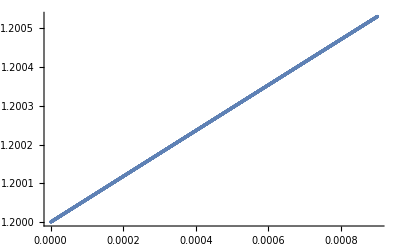

```mathematica
LLL=12;
Table[{ϵ,(Det[%319]/Det[%320])},{ϵ,.0009,0.0000011,-.00000013}]//ListPlot
```

```mathematica
LLL^2/(LLL (LLL-2.))
```

1.2

```mathematica
2 13^2
```

338

```mathematica
336/14
```

24

```mathematica
GGpx=GGp/.{GGp[[2]]->GGp[[2]](*+GGp[[1]]*)};
GGpxx=GGpx/.{GGpx[[3]]->GGpx[[3]]+GGpx[[2]]};
(*GGpxxx=GGpxx/.{GGpxx[[4]]->GGpxx[[4]]+GGpxx[[3]]};*)
GGpT=Transpose[GGpxx];
(*GGpTx=GGpT/.{GGpT[[2]]->GGpT[[2]]+GGpT[[1]]};
GGpTxx=GGpTx/.{GGpTx[[3]]->GGpTx[[3]]+GGpTx[[2]]};
(*GGpTxxx=GGpTxx/.{GGpTxx[[4]]->GGpTxx[[4]]+GGpTxx[[3]]};*)*)
GGpfin=Transpose[GGpT];
MatrixForm[FullSimplify[GGpxx]]
```

1/(1-(1+ϵ-ⅈ ϵp)^2)+1/(1-(-1+ϵ+ⅈ ϵpp)^2)

```mathematica
FullSimplify[4D[ArcTan[xxx/8],xxx]]
```

```mathematica
FullSimplify[2 (1/(1-(1+ϵ-ⅈ ϵp)^2)+1/(1-(ϵ+ⅈ ϵp)^2))-2/(1-(1+ϵ-ⅈ ϵp)^2)+2/(-1+ϵ^2+2 ⅈ ϵ ϵp-ϵp^2)+LLL/(ⅈ ϵp+ϵp^2)-2/(1+(ⅈ-ϵp+ϵpp)^2)-2/(1+(2 ⅈ+ϵp+ϵpp)^2)+2 (1/(1+(ⅈ-ϵp+ϵpp)^2)+1/(1+(2 ⅈ+ϵp+ϵpp)^2))]
```

LLL/(ⅈ ϵp+ϵp^2)

```mathematica
Det[GGp]
```

(-(-ϵ+ϵpp) ((ϵ+ϵ^2) (ϵ+ϵp) (2+ϵ+ϵp)^2 (ϵp+ϵp^2) (-2+ϵ-ϵpp) (-2+ϵp-ϵpp) (ϵp-ϵpp)+(ϵ+ϵ^2) (ϵ+ϵp)^2 (2+ϵ+ϵp)^2 (ϵp+ϵp^2) (-2+ϵ-ϵpp) (ϵ-ϵpp) (-2+ϵp-ϵpp) (-LLL/(ϵ+ϵ^2)+2 (1/((ϵ+ϵp) (2+ϵ+ϵp))+1/(ϵ^2-2 ϵ (1+ϵpp)+ϵpp (2+ϵpp)))))+(-ϵp+ϵpp) (-(ϵ+ϵ^2) (ϵ+ϵp) (2+ϵ+ϵp)^2 (ϵp+ϵp^2) (-2+ϵ-ϵpp) (ϵ-ϵpp) (-2+ϵp-ϵpp)-(ϵ+ϵ^2) (ϵ+ϵp)^2 (2+ϵ+ϵp)^2 (ϵp+ϵp^2) (-2+ϵ-ϵpp) (-2+ϵp-ϵpp) (ϵp-ϵpp) (-LLL/(ϵp+ϵp^2)+2 (1/((ϵ+ϵp) (2+ϵ+ϵp))+1/(ϵp^2-2 ϵp (1+ϵpp)+ϵpp (2+ϵpp)))))+(ϵ+ϵp-2 ϵpp) (-(ϵ+ϵ^2) (2+ϵ+ϵp)^2 (ϵp+ϵp^2) (-2+ϵ-ϵpp) (ϵ-ϵpp) (-2+ϵp-ϵpp) (ϵp-ϵpp)+(ϵ+ϵ^2) (ϵ+ϵp)^2 (2+ϵ+ϵp)^2 (ϵp+ϵp^2) (-2+ϵ-ϵpp) (ϵ-ϵpp) (-2+ϵp-ϵpp) (ϵp-ϵpp) (-LLL/(ϵ+ϵ^2)+2 (1/((ϵ+ϵp) (2+ϵ+ϵp))+1/(ϵ^2-2 ϵ (1+ϵpp)+ϵpp (2+ϵpp)))) (-LLL/(ϵp+ϵp^2)+2 (1/((ϵ+ϵp) (2+ϵ+ϵp))+1/(ϵp^2-2 ϵp (1+ϵpp)+ϵpp (2+ϵpp))))))/((ϵ+ϵ^2) (ϵ+ϵp)^2 (2+ϵ+ϵp)^2 (ϵp+ϵp^2) (-2+ϵ-ϵpp) (ϵ-ϵpp)^2 (-2+ϵp-ϵpp) (ϵp-ϵpp) (-ϵp+ϵpp))

```mathematica
FullSimplify[Series[%2325,{ϵ,0,0},{ϵp,0,0},{ϵpp,0,0}]]
```

(((2 (-1+LLL) LLL)/ϵpp-1/6 (-1+LLL) LLL (-2+3 LLL)+O[ϵpp]^1)/ϵp+(((-2+LLL) LLL)/ϵpp^2+((28-9 LLL) LLL)/(6 ϵpp)+1/18 LLL (58+LLL (-61+9 LLL))+O[ϵpp]^1)+O[ϵp]^1)/ϵ+((((-2+LLL) LLL)/ϵpp^2+((46-9 LLL) LLL)/(6 ϵpp)+1/18 LLL (94+LLL (-79+9 LLL))+O[ϵpp]^1)/ϵp+(-(2 LLL)/ϵpp^3+((23-6 LLL) LLL)/(3 ϵpp^2)+(-(89 LLL)/18+LLL^2)/ϵpp-1/108 LLL (2368-777 LLL+54 LLL^2)+O[ϵpp]^1)+O[ϵp]^1)+O[ϵ]^1

```mathematica
FullSimplify[(-2/(1+(-ⅈ/2+rrr[1])^2)-2/(1+(ⅈ/2+rrr[1])^2)-2/(1+(-(3 ⅈ)/2+rrr[1])^2)-2/(1+((3 ⅈ)/2+rrr[1])^2)-2/(1+(-ⅈ/2+rrr[2])^2)-2/(1+(ⅈ/2+rrr[2])^2)-2/(1+(-(3 ⅈ)/2+rrr[2])^2)-2/(1+((3 ⅈ)/2+rrr[2])^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2)-2/(1+(-(3 ⅈ)/2+rrr[3])^2)-2/(1+((3 ⅈ)/2+rrr[3])^2)-2/(1+(-ⅈ/2+rrr[4])^2)-2/(1+(ⅈ/2+rrr[4])^2)-2/(1+(-(3 ⅈ)/2+rrr[4])^2)-2/(1+((3 ⅈ)/2+rrr[4])^2))/.{rrr[1]->xxx/2-3/2I,rrr[2]->xxx/2-I/2,rrr[3]->xxx/2+I/2,rrr[4]->xxx/2+3/2I}]
```

16 (-1/(4+xxx^2)-2/(16+xxx^2)-3/(36+xxx^2)-2/(64+xxx^2))

```mathematica
FullSimplify[-2/(1+(-ⅈ+xxx/2)^2)-2/(1+(ⅈ+xxx/2)^2)]
```

-16/(16+xxx^2)

```mathematica
n=3;
λ=Table[rrr/2+I/2(n+1-2j),{j,1,n}]
```

{ⅈ+rrr/2,rrr/2,-ⅈ+rrr/2}

```mathematica
FullSimplify[GGp[[1]]+GGp[[2]]]
```

{-LLL/(ϵ+ϵ^2),-LLL/(2+3 ϵp+ϵp^2)}

```mathematica
FullSimplify[2/(ϵ^2-2 ϵ (1+ϵp)+ϵp (2+ϵp))+2/(ϵp^2-2 ϵp (1+ϵpp)+ϵpp (2+ϵpp))+1/(ϵp-ϵpp)]
```

2/((-2+ϵ-ϵp) (ϵ-ϵp))+1/(-2+ϵp-ϵpp)

```mathematica
GGp1x=GGp/.{GGp[[2]]->GGp[[1]]+GGp[[2]]+GGp[[3]]};
GGp1xx=GGp1x/.{GGp[[2]]->GGp[[2]]+GGp[[3]]};
GGp1T=Transpose[GGp1xx];
GGp1Tx=GGp1T/.{GGp1T[[1]]->GGp1T[[1]]+GGp1T[[2]]+GGp1T[[3]]};
GGp1Txx=GGp1Tx/.{GGp1T[[2]]->GGp1T[[2]]+GGp1T[[3]]};
GGpfin=Transpose[GGp1Txx];
MatrixForm[GGp1Txx]
```

(LLL/(1/4+rrr[1]^2)-2/(1+(-ⅈ/2+rrr[1])^2)-2/(1+(ⅈ/2+rrr[1])^2)+LLL/(1/4+rrr[2]^2)-2/(1+(-ⅈ/2+rrr[2])^2)-2/(1+(ⅈ/2+rrr[2])^2)+LLL/(1/4+rrr[3]^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2) | LLL/(1/4+rrr[2]^2)-2/(1+(-ⅈ/2+rrr[2])^2)-2/(1+(ⅈ/2+rrr[2])^2)+LLL/(1/4+rrr[3]^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2) | LLL/(1/4+rrr[3]^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2)
2/(1+(rrr[1]-rrr[2])^2)+LLL/(1/4+rrr[2]^2)-2/(1+(-ⅈ/2+rrr[2])^2)-2/(1+(ⅈ/2+rrr[2])^2)-2/(1+(-rrr[1]+rrr[2])^2)+2/(1+(rrr[1]-rrr[3])^2)+LLL/(1/4+rrr[3]^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2)-2/(1+(-rrr[1]+rrr[3])^2) | LLL/(1/4+rrr[2]^2)-2/(1+(-ⅈ/2+rrr[2])^2)-2/(1+(ⅈ/2+rrr[2])^2)-2/(1+(-rrr[1]+rrr[2])^2)-2/(1+(rrr[1]+rrr[2])^2)+LLL/(1/4+rrr[3]^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2)-2/(1+(-rrr[1]+rrr[3])^2)-2/(1+(rrr[1]+rrr[3])^2) | LLL/(1/4+rrr[3]^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2)-2/(1+(-rrr[1]+rrr[3])^2)-2/(1+(rrr[1]+rrr[3])^2)
2/(1+(rrr[1]-rrr[3])^2)+2/(1+(rrr[2]-rrr[3])^2)+LLL/(1/4+rrr[3]^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2)-2/(1+(-rrr[1]+rrr[3])^2)-2/(1+(-rrr[2]+rrr[3])^2) | 2/(1+(rrr[2]-rrr[3])^2)+LLL/(1/4+rrr[3]^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2)-2/(1+(-rrr[1]+rrr[3])^2)-2/(1+(rrr[1]+rrr[3])^2)-2/(1+(-rrr[2]+rrr[3])^2) | LLL/(1/4+rrr[3]^2)-2/(1+(-ⅈ/2+rrr[3])^2)-2/(1+(ⅈ/2+rrr[3])^2)-2/(1+(-rrr[1]+rrr[3])^2)-2/(1+(rrr[1]+rrr[3])^2)-2/(1+(-rrr[2]+rrr[3])^2)-2/(1+(rrr[2]+rrr[3])^2))

```mathematica
GGm1x=GGm/.{GGm[[1]]->GGm[[1]]+GGm[[2]]+GGm[[3]]+GGm[[4]]};
GGm1xx=GGm1x/.{GGm[[2]]->GGm[[2]]+GGm[[3]]+GGm[[4]]};
GGm1xxx=GGm1xx/.{GGm[[3]]->GGm[[3]]+GGm[[4]]};
GGm1T=Transpose[GGm1xxx];
GGm1Tx=GGm1T/.{GGm1T[[1]]->GGm1T[[1]]+GGm1T[[2]]+GGm1T[[3]]+GGm1T[[4]]};
GGm1Txx=GGm1Tx/.{GGm1T[[2]]->GGm1T[[2]]+GGm1T[[3]]+GGm1T[[4]]};
GGm1Txxx=GGm1Txx/.{GGm1T[[3]]->GGm1T[[3]]+GGm1T[[4]]};
GGmfin=Transpose[GGm1Txxx];
MatrixForm[FullSimplify[GGm1Txxx]]
```

(1/(ϵ+ϵ^2)+8/((1+ϵ+ϵp) (3+ϵ+ϵp))+1/(2+3 ϵp+ϵp^2)+8/((2+ϵ+ϵpp) (4+ϵ+ϵpp))+8/((3+ϵp+ϵpp) (5+ϵp+ϵpp))+1/(6+5 ϵpp+ϵpp^2)+1/(3+ϵppp)-1/(4+ϵppp)+4/(3+ϵ+ϵppp)-4/(5+ϵ+ϵppp)+4/(4+ϵp+ϵppp)-4/(6+ϵp+ϵppp)+4/(5+ϵpp+ϵppp)-4/(7+ϵpp+ϵppp)+LLL (-1/(ϵ+ϵ^2)-1/(2+3 ϵp+ϵp^2)-1/(6+5 ϵpp+ϵpp^2)-1/(3+ϵppp)+1/(4+ϵppp)) | 4/((1+ϵ+ϵp) (3+ϵ+ϵp))+1/(2+3 ϵp+ϵp^2)-LLL/(2+3 ϵp+ϵp^2)+4/((2+ϵ+ϵpp) (4+ϵ+ϵpp))+8/((3+ϵp+ϵpp) (5+ϵp+ϵpp))+1/(6+5 ϵpp+ϵpp^2)-LLL/(6+5 ϵpp+ϵpp^2)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+2/(3+ϵ+ϵppp)-2/(5+ϵ+ϵppp)+4/(4+ϵp+ϵppp)-4/(6+ϵp+ϵppp)+4/(5+ϵpp+ϵppp)-4/(7+ϵpp+ϵppp) | 4/((2+ϵ+ϵpp) (4+ϵ+ϵpp))+4/((3+ϵp+ϵpp) (5+ϵp+ϵpp))+1/(6+5 ϵpp+ϵpp^2)-LLL/(6+5 ϵpp+ϵpp^2)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+2/(3+ϵ+ϵppp)-2/(5+ϵ+ϵppp)+2/(4+ϵp+ϵppp)-2/(6+ϵp+ϵppp)+4/(5+ϵpp+ϵppp)-4/(7+ϵpp+ϵppp) | (1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+2/(3+ϵ+ϵppp)-2/(5+ϵ+ϵppp)+2/(4+ϵp+ϵppp)-2/(6+ϵp+ϵppp)+2/(5+ϵpp+ϵppp)-2/(7+ϵpp+ϵppp)
4/((1+ϵ+ϵp) (3+ϵ+ϵp))+1/(2+3 ϵp+ϵp^2)-LLL/(2+3 ϵp+ϵp^2)+4/((2+ϵ+ϵpp) (4+ϵ+ϵpp))+8/((3+ϵp+ϵpp) (5+ϵp+ϵpp))+1/(6+5 ϵpp+ϵpp^2)-LLL/(6+5 ϵpp+ϵpp^2)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+2/(3+ϵ+ϵppp)-2/(5+ϵ+ϵppp)+4/(4+ϵp+ϵppp)-4/(6+ϵp+ϵppp)+4/(5+ϵpp+ϵppp)-4/(7+ϵpp+ϵppp) | 2/((-ϵ+ϵp) (2-ϵ+ϵp))+2/((1+ϵ+ϵp) (3+ϵ+ϵp))+1/(2+3 ϵp+ϵp^2)-LLL/(2+3 ϵp+ϵp^2)+2/((-3+ϵ-ϵpp) (-1+ϵ-ϵpp))+2/((2+ϵ+ϵpp) (4+ϵ+ϵpp))+8/((3+ϵp+ϵpp) (5+ϵp+ϵpp))+1/(6+5 ϵpp+ϵpp^2)-LLL/(6+5 ϵpp+ϵpp^2)+1/(-4+ϵ-ϵppp)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+1/(2-ϵ+ϵppp)+1/(3+ϵ+ϵppp)-1/(5+ϵ+ϵppp)+4/(4+ϵp+ϵppp)-4/(6+ϵp+ϵppp)+4/(5+ϵpp+ϵppp)-4/(7+ϵpp+ϵppp) | 2/((1-ϵ+ϵpp) (3-ϵ+ϵpp))+2/((2+ϵ+ϵpp) (4+ϵ+ϵpp))+4/((3+ϵp+ϵpp) (5+ϵp+ϵpp))+1/(6+5 ϵpp+ϵpp^2)-LLL/(6+5 ϵpp+ϵpp^2)+1/(-4+ϵ-ϵppp)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+1/(2-ϵ+ϵppp)+1/(3+ϵ+ϵppp)-1/(5+ϵ+ϵppp)+2/(4+ϵp+ϵppp)-2/(6+ϵp+ϵppp)+4/(5+ϵpp+ϵppp)-4/(7+ϵpp+ϵppp) | 1/(-4+ϵ-ϵppp)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+1/(2-ϵ+ϵppp)+1/(3+ϵ+ϵppp)-1/(5+ϵ+ϵppp)+2/(4+ϵp+ϵppp)-2/(6+ϵp+ϵppp)+2/(5+ϵpp+ϵppp)-2/(7+ϵpp+ϵppp)
4/((2+ϵ+ϵpp) (4+ϵ+ϵpp))+4/((3+ϵp+ϵpp) (5+ϵp+ϵpp))+1/(6+5 ϵpp+ϵpp^2)-LLL/(6+5 ϵpp+ϵpp^2)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+2/(3+ϵ+ϵppp)-2/(5+ϵ+ϵppp)+2/(4+ϵp+ϵppp)-2/(6+ϵp+ϵppp)+4/(5+ϵpp+ϵppp)-4/(7+ϵpp+ϵppp) | 2/((1-ϵ+ϵpp) (3-ϵ+ϵpp))+2/((2+ϵ+ϵpp) (4+ϵ+ϵpp))+4/((3+ϵp+ϵpp) (5+ϵp+ϵpp))+1/(6+5 ϵpp+ϵpp^2)-LLL/(6+5 ϵpp+ϵpp^2)+1/(-4+ϵ-ϵppp)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+1/(2-ϵ+ϵppp)+1/(3+ϵ+ϵppp)-1/(5+ϵ+ϵppp)+2/(4+ϵp+ϵppp)-2/(6+ϵp+ϵppp)+4/(5+ϵpp+ϵppp)-4/(7+ϵpp+ϵppp) | 2/((1-ϵ+ϵpp) (3-ϵ+ϵpp))+2/((2+ϵ+ϵpp) (4+ϵ+ϵpp))+2/((-ϵp+ϵpp) (2-ϵp+ϵpp))+2/((3+ϵp+ϵpp) (5+ϵp+ϵpp))+1/(6+5 ϵpp+ϵpp^2)-LLL/(6+5 ϵpp+ϵpp^2)+1/(-4+ϵ-ϵppp)+1/(-3+ϵp-ϵppp)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+1/(2-ϵ+ϵppp)+1/(3+ϵ+ϵppp)-1/(5+ϵ+ϵppp)+1/(1-ϵp+ϵppp)+1/(4+ϵp+ϵppp)-1/(6+ϵp+ϵppp)+4/(5+ϵpp+ϵppp)-4/(7+ϵpp+ϵppp) | 1/(-4+ϵ-ϵppp)+1/(-3+ϵp-ϵppp)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+1/(2-ϵ+ϵppp)+1/(3+ϵ+ϵppp)-1/(5+ϵ+ϵppp)+1/(1-ϵp+ϵppp)+1/(4+ϵp+ϵppp)-1/(6+ϵp+ϵppp)+2/(5+ϵpp+ϵppp)-2/(7+ϵpp+ϵppp)
(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+2/(3+ϵ+ϵppp)-2/(5+ϵ+ϵppp)+2/(4+ϵp+ϵppp)-2/(6+ϵp+ϵppp)+2/(5+ϵpp+ϵppp)-2/(7+ϵpp+ϵppp) | 1/(-4+ϵ-ϵppp)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+1/(2-ϵ+ϵppp)+1/(3+ϵ+ϵppp)-1/(5+ϵ+ϵppp)+2/(4+ϵp+ϵppp)-2/(6+ϵp+ϵppp)+2/(5+ϵpp+ϵppp)-2/(7+ϵpp+ϵppp) | 1/(-4+ϵ-ϵppp)+1/(-3+ϵp-ϵppp)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+1/(2-ϵ+ϵppp)+1/(3+ϵ+ϵppp)-1/(5+ϵ+ϵppp)+1/(1-ϵp+ϵppp)+1/(4+ϵp+ϵppp)-1/(6+ϵp+ϵppp)+2/(5+ϵpp+ϵppp)-2/(7+ϵpp+ϵppp) | 1/(-4+ϵ-ϵppp)+1/(-3+ϵp-ϵppp)+1/(-2+ϵpp-ϵppp)+(1-LLL)/(3+ϵppp)+(-1+LLL)/(4+ϵppp)+1/(2-ϵ+ϵppp)+1/(3+ϵ+ϵppp)-1/(5+ϵ+ϵppp)+1/(1-ϵp+ϵppp)+1/(4+ϵp+ϵppp)-1/(6+ϵp+ϵppp)+1/(-ϵpp+ϵppp)+1/(5+ϵpp+ϵppp)-1/(7+ϵpp+ϵppp))

```mathematica
FullSimplify[ϵ^2-2 ϵ (1+ϵp)+ϵp (2+ϵp)]
```

(-2+ϵ-ϵp) (ϵ-ϵp)

```mathematica
MatrixForm[%895/.{ϵ->0,ϵp->0,ϵpp->0,ϵppp->0}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

(ComplexInfinity | -(3 LLL)/4 | -LLL/4 | -LLL/12
-(3 LLL)/4 | ComplexInfinity | 13/10-LLL/4 | 23/60-LLL/12
-LLL/4 | 13/10-LLL/4 | ComplexInfinity | 17/15-LLL/12
-LLL/12 | 23/60-LLL/12 | 17/15-LLL/12 | ComplexInfinity)

```mathematica
8/7.
```

1.14286

```mathematica
MatrixForm[ {{LLL/(1/4 - (1/2 + ϵ)^2) - 2/(
   1 + (I (1/2 + ϵ) - I (1/2 + ϵp))^2) - 2/(
   1 + (I (1/2 + ϵ) + I (1/2 + ϵp))^2) - 2/(
   1 + (I (1/2 + ϵ) - I (3/2 + ϵpp))^2) - 2/(
   1 + (I (1/2 + ϵ) + I (3/2 + ϵpp))^2), 
  2/(1 + (I (1/2 + ϵ) - I (1/2 + ϵp))^2) + 2/(
   1 + (I (1/2 + ϵ) + I (1/2 + ϵp))^2), 
  2/(1 + (I (1/2 + ϵ) - I (3/2 + ϵpp))^2) + 2/(
   1 + (I (1/2 + ϵ) + I (3/2 + ϵpp))^2)}, {2/(
   1 + (-I (1/2 + ϵ) + I (1/2 + ϵp))^2) + 2/(
   1 + (I (1/2 + ϵ) + I (1/2 + ϵp))^2), 
  LLL/(1/4 - (1/2 + ϵp)^2) - 2/(
   1 + (-I (1/2 + ϵ) + I (1/2 + ϵp))^2) - 2/(
   1 + (I (1/2 + ϵ) + I (1/2 + ϵp))^2) - 2/(
   1 + (I (1/2 + ϵp) - I (3/2 + ϵpp))^2) - 2/(
   1 + (I (1/2 + ϵp) + I (3/2 + ϵpp))^2), 
  2/(1 + (I (1/2 + ϵp) - I (3/2 + ϵpp))^2) + 2/(
   1 + (I (1/2 + ϵp) + I (3/2 + ϵpp))^2)}, {2/(
   1 + (-I (1/2 + ϵ) + I (3/2 + ϵpp))^2) + 2/(
   1 + (I (1/2 + ϵ) + I (3/2 + ϵpp))^2), 
  2/(1 + (-I (1/2 + ϵp) + I (3/2 + ϵpp))^2) + 2/(
   1 + (I (1/2 + ϵp) + I (3/2 + ϵpp))^2), 
  LLL/(1/4 - (3/2 + ϵpp)^2) - 2/(
   1 + (-I (1/2 + ϵ) + I (3/2 + ϵpp))^2) - 2/(
   1 + (I (1/2 + ϵ) + I (3/2 + ϵpp))^2) - 2/(
   1 + (-I (1/2 + ϵp) + I (3/2 + ϵpp))^2) - 2/(
   1 + (I (1/2 + ϵp) + I (3/2 + ϵpp))^2)}}]
```

(LLL/(1/4-(1/2+ϵ)^2)-2/(1+(ⅈ (1/2+ϵ)-ⅈ (1/2+ϵp))^2)-2/(1+(ⅈ (1/2+ϵ)+ⅈ (1/2+ϵp))^2)-2/(1+(ⅈ (1/2+ϵ)-ⅈ (3/2+ϵpp))^2)-2/(1+(ⅈ (1/2+ϵ)+ⅈ (3/2+ϵpp))^2) | 2/(1+(ⅈ (1/2+ϵ)-ⅈ (1/2+ϵp))^2)+2/(1+(ⅈ (1/2+ϵ)+ⅈ (1/2+ϵp))^2) | 2/(1+(ⅈ (1/2+ϵ)-ⅈ (3/2+ϵpp))^2)+2/(1+(ⅈ (1/2+ϵ)+ⅈ (3/2+ϵpp))^2)
2/(1+(-ⅈ (1/2+ϵ)+ⅈ (1/2+ϵp))^2)+2/(1+(ⅈ (1/2+ϵ)+ⅈ (1/2+ϵp))^2) | LLL/(1/4-(1/2+ϵp)^2)-2/(1+(-ⅈ (1/2+ϵ)+ⅈ (1/2+ϵp))^2)-2/(1+(ⅈ (1/2+ϵ)+ⅈ (1/2+ϵp))^2)-2/(1+(ⅈ (1/2+ϵp)-ⅈ (3/2+ϵpp))^2)-2/(1+(ⅈ (1/2+ϵp)+ⅈ (3/2+ϵpp))^2) | 2/(1+(ⅈ (1/2+ϵp)-ⅈ (3/2+ϵpp))^2)+2/(1+(ⅈ (1/2+ϵp)+ⅈ (3/2+ϵpp))^2)
2/(1+(-ⅈ (1/2+ϵ)+ⅈ (3/2+ϵpp))^2)+2/(1+(ⅈ (1/2+ϵ)+ⅈ (3/2+ϵpp))^2) | 2/(1+(-ⅈ (1/2+ϵp)+ⅈ (3/2+ϵpp))^2)+2/(1+(ⅈ (1/2+ϵp)+ⅈ (3/2+ϵpp))^2) | LLL/(1/4-(3/2+ϵpp)^2)-2/(1+(-ⅈ (1/2+ϵ)+ⅈ (3/2+ϵpp))^2)-2/(1+(ⅈ (1/2+ϵ)+ⅈ (3/2+ϵpp))^2)-2/(1+(-ⅈ (1/2+ϵp)+ⅈ (3/2+ϵpp))^2)-2/(1+(ⅈ (1/2+ϵp)+ⅈ (3/2+ϵpp))^2))